```mathematica
(* Stability analysis of continous logistic *)
Clear["Global`*"]
(* Specify some parameter values for plotting *)
parms={r->1,K->2}
```

{r→1,K→2}

```mathematica
(* Define model as differential eqn. *)
dNdt=r N (1-N/K)
```

N (1-N/K) r

```mathematica
(* Solve for equilibria *)
equil=Solve[dNdt==0,N]
```

{{N→0},{N→K}}

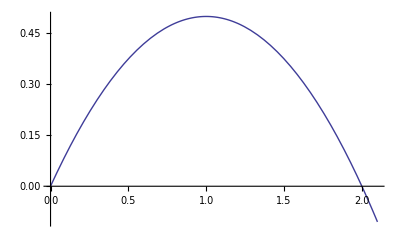

```mathematica
Plot[dNdt/.parms,{N,0,2.1}]
```

```mathematica
(* Calculate first derivative of model w.r.t. N *)
D[dNdt,N]
Simplify[%]
```

-(N r)/K+(1-N/K) r

r-(2 N r)/K

```mathematica
(* Define first derivative of the model w.r.t. N*)
DdNdt[N_]:=Simplify[D[dNdt,N]]
(* test the function *)
DdNdt[N]
```

r-(2 N r)/K

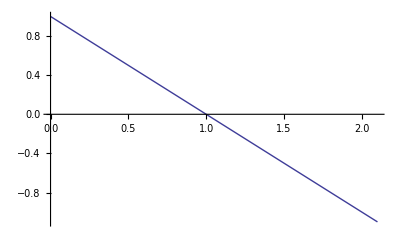

```mathematica
Plot[%/.parms,{N,0,2.1}]
```

```mathematica
(* Evaluate first derivative each equilibrium *)
DdNdt[N]/.N->0
DdNdt[N]/.N->K
```

r

-r

```mathematica
(* Evaluate first derivative at both equilibria together *)
DdNdt[N]/.equil
```

{r,-r}

```mathematica
(* System Potential *)
pN=-Integrate[dNdt,N]
```

-(N^2/2-N^3/(3 K)) r

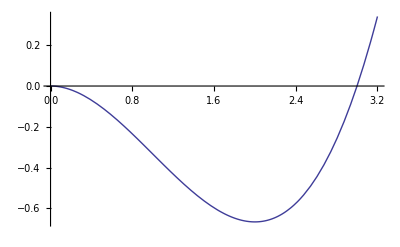

```mathematica
Plot[pN/.parms,{N,0,3.2}]
```